## Split stage filtering

The envelope follower of a compressor is a starting point for a two stage filter that maintains the gain of a positive-valued input signal by filtering the release stage (decreasing input value) before the attack stage (increasing input value)

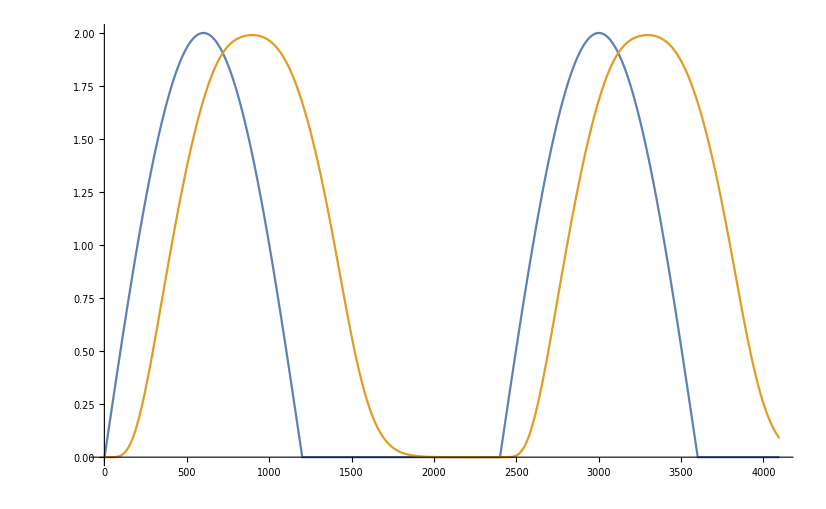

```mathematica
releaseOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]

(* preserve gradient version *)
releaseOnlySVFPG[X_,fc_,Q_,sr_]:=Module[{prevY1,prevY2,gInv,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0 / g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY1 = 0;
prevY2 =0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY1, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0.5*(prevY1-prevY2)*gInv; ic2=prevY1];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY2 = prevY1;
prevY1= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


ordinarySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,

(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

output
]

EnvelopeProcessSeparateTriple[X_, attackFc_, releaseFc_]:=Module[{fMultiplier,Q,sampleRate,output},
sampleRate = 48000;
Q=0.5;
fMultiplier = 1.5;

output = X;


output =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[output,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate];

(*
output = attackOnlySVF[
		attackOnlySVF[
		attackOnlySVF[output,attackFc fMultiplier,Q,sampleRate],
		attackFc fMultiplier,Q,sampleRate],
		attackFc fMultiplier,Q,sampleRate]; 
*)


output = ordinarySVF[
		ordinarySVF[
		ordinarySVF[output,attackFc fMultiplier,Q,sampleRate],
		attackFc fMultiplier,Q,sampleRate],
		attackFc fMultiplier,Q,sampleRate]; 


output
]

sampleRate = 48000;
length = 2^12;
input = Table[Sin[20 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];

 ListLinePlot[{input+Abs[input],EnvelopeProcessSeparateTriple[input+Abs[input],150,150]}]
```